# Drugi kviz

Vsaka podnaloga je vredna 1 točko, razen če je pri podnalogi zapisano drugače. Skupno je moč doseči 20 točk.

## Naloga 1

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi produkt indeksa stolpca in indeksa vrstice (začnemo šteti z 1).

```mathematica
A[n_,m_]:=Table[i*j,{i,1,n},{j,1,m}]
```

b) Pokažite, da je  simetrična matrika.

```mathematica
A =A[10, 10]
```

{{1,2,3,4,5,6,7,8,9,10},{2,4,6,8,10,12,14,16,18,20},{3,6,9,12,15,18,21,24,27,30},{4,8,12,16,20,24,28,32,36,40},{5,10,15,20,25,30,35,40,45,50},{6,12,18,24,30,36,42,48,54,60},{7,14,21,28,35,42,49,56,63,70},{8,16,24,32,40,48,56,64,72,80},{9,18,27,36,45,54,63,72,81,90},{10,20,30,40,50,60,70,80,90,100}}

c) Izračunajte lastne vrednosti in lastne vektorje matrike .

```mathematica
matrix=A[10,10];
eigenvalues=Eigenvalues[matrix];
eigenvectors=Eigenvectors[matrix];
```

d) Izračunajte karakteristični polinom matrike .

```mathematica
A10=A[10,10];
charPoly=CharacteristicPolynomial[A10,λ]
```

CharacteristicPolynomial[{{1,2,3,4,5,6,7,8,9,10},{2,4,6,8,10,12,14,16,18,20},{3,6,9,12,15,18,21,24,27,30},{4,8,12,16,20,24,28,32,36,40},{5,10,15,20,25,30,35,40,45,50},{6,12,18,24,30,36,42,48,54,60},{7,14,21,28,35,42,49,56,63,70},{8,16,24,32,40,48,56,64,72,80},{9,18,27,36,45,54,63,72,81,90},{10,20,30,40,50,60,70,80,90,100}}[10,10],λ]

e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .

```mathematica
{eigenvalues,eigenvectors}=Eigensystem[A10];
P=eigenvectors;
G=DiagonalMatrix[eigenvalues];
```

Set::shape: Lists {eigenvalues,eigenvectors} and Eigensystem[A10] are not the same shape.

f) (2 točki) Rešite matrično enačbo .

```mathematica
I=IdentityMatrix[10];
X=LinearSolve[A10+P-G,I]
```

Set::wrsym: Symbol ⅈ is Protected.

LinearSolve[A10-G+P,ⅈ]

g) Ali je matrika  obrnljiva?

```mathematica
detA=Determinant[A10];
invertibleQ=detA!=0
```

Determinant[{{1,2,3,4,5,6,7,8,9,10},{2,4,6,8,10,12,14,16,18,20},{3,6,9,12,15,18,21,24,27,30},{4,8,12,16,20,24,28,32,36,40},{5,10,15,20,25,30,35,40,45,50},{6,12,18,24,30,36,42,48,54,60},{7,14,21,28,35,42,49,56,63,70},{8,16,24,32,40,48,56,64,72,80},{9,18,27,36,45,54,63,72,81,90},{10,20,30,40,50,60,70,80,90,100}}[10,10]]≠0

## Naloga 2

Imamo klančino z naklonom 20 stopinj dolžine 5m. Na dnu klančine se nahaja ravnina dolžine 10m.
Kroglico z radijem 20cm potisnemo s skrajno desnega roba ravnine s hitrostjo v0 = 11m/s. Ko pride kroglica na vrh klančine, skoči čez rob, dokler ne pristane na tleh (poševni met). 
Predpostavite lahko, da med kroglico in podlago ni trenja in da se zaradi kotaljenja energija ne izgublja. Simulirajte gibanje kroglice do trenutka ko pristane na tleh.
Za gravitacijski pospešek vzemite g = 9.81 m/s^2, za simulacijo pa vzemite  . (Glej sliko).

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, dolžino podlage, začetno hitrost in radij kroglice.

```mathematica
g=9.81;
naklon=20 Degree;
L=5;
D=10;
v0=11;
r=0.2;
```

b) Nariši klančino in tla.

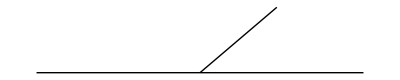

```mathematica
Graphics[{Line[{{0,0},{20,0}}],Line[{{10,0},{10+5*Cos[20 Degree],5*Sin[20 Degree]}}]}]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče (Uporabi `Dynamic`).

```mathematica
DynamicModule[{cx=2,cy=0.5},Graphics[{Line[{{0,0},{20,0}}],Line[{{10,0},{10+5*Cos[20 Degree],5*Sin[20 Degree]}}],Style[Disk[{cx,cy},0.5],Blue]},PlotRange->{{0,20},{-5,5}},Axes->True,Dynamic[cx,cy]]]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
naKlancu[x_,y_,L_,h_]:=If[x<=L&&y>=h,True,False]
```

e) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α po času Δt.

```mathematica
posodobiHitrost[v_,α_,Δt_]:=Module[{vx,vy,g=9.81,ax,ay},vx=v[[1]];
vy=v[[2]];
ax=0;]
```

f) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[v_,alpha_]:=Module[{vX,vY,g,vKlanecX,vKlanecY},g=9.81;
{vX,vY}=v;
vKlanecX=vX*Cos[alpha]+vY*Sin[alpha];
vKlanecY=vY*Cos[alpha]-vX*Sin[alpha];
{vKlanecX,vKlanecY}]
```

g) Definiraj funkcijo `posodobiHitrostPosevniMet`, ki sprejme trenutno hitrost kroglice in vrne novo hitrost kroglice po času Δt.

```mathematica
posodobiHitrostPosevniMet[v_,deltaT_]:=Module[{g,vX,vY,vYnova},g=9.81;
{vX,vY}=v;
vYnova=vY-g*deltaT;
{vX,vYnova}]
```

h) Definiraj funkcijo `posodobiLego`, ki sprejme trenutno lego kroglice in njeno hitrost in vrne novo lego kroglice po času Δt.

```mathematica
posodobiLego[lego_,v_,deltaT_]:=Module[{x,y,vX,vY,novoX,novoY},{x,y}=lego;
{vX,vY}=v;
novoX=x+vX*deltaT;
novoY=y+vY*deltaT;
{novoX,novoY}]
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice. (4 točke - gibanje po ravnini (1 točka), gibanje po klančini (1 točka), gibanje pri poševnem metu (1 točka), simulacija se ustavi, ko žogica pristane na tleh (1 točka))